```mathematica
μ/(μ+ν)==p
```

```mathematica
(ν+μ t/(1/δ(1-E^(-δ t))))/(ν+μ)//Simplify
```

((t δ μ)/(1-ⅇ^(-t δ))+ν)/(μ+ν)

```mathematica
Solve[((t δ μ)/(1-ⅇ^(-t δ))+ν)/(μ+ν)==ω,μ]//Simplify
```

{{μ→((-1+ⅇ^(t δ)) ν (-1+ω))/(ⅇ^(t δ) (t δ-ω)+ω)}}

```mathematica
1-(((-1+ⅇ^(t δ))(-1+ω))/(ⅇ^(t δ) (t δ-ω)+ω)+1)^(-1)//FullSimplify
```

((-1+ⅇ^(t δ)) (-1+ω))/(1+ⅇ^(t δ) (-1+t δ))

```mathematica
(ν+μ/(1-δ t/2+θ))/(ν+μ)//FullSimplify
```

(μ/(1-(t δ)/2+θ)+ν)/(μ+ν)

```mathematica
Solve[ω==(ν+μ/(1-δ t/2+θ))/(ν+μ),μ]/.{θ->0}//Simplify
```

{{μ→-((-2+t δ) ν (-1+ω))/(2+(-2+t δ) ω)}}

```mathematica
μ/ν==-(ω-1)/(ω+1/(δ t/2 - 1))//FullSimplify
```

1+μ/ν==(t δ)/(2-2 ω+t δ ω)

```mathematica
1-((t δ)/(2-2 ω+t δ ω))^-1//FullSimplify
```

-((-2+t δ) (-1+ω))/(t δ)

```mathematica
Solve[ω==(ν+μ δ t)/(ν+μ),μ]
```

{{μ→-(ν (-1+ω))/(-t δ+ω)}}

```mathematica
Solve[p/(1-p)==μ/ν,p]
```

{{p→μ/(μ+ν)}}

```mathematica
1-(-(-1+ω)/(-t δ+ω)+1)^(-1)//Simplify
```

(-1+ω)/(-1+t δ)

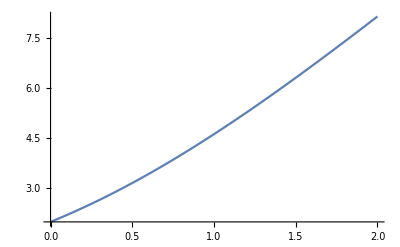

```mathematica
Plot[δ μ t/(1-E^(-δ t))/.{μ->2,δ->2},{t,0,2}]
```

```mathematica
ωF[t_,ν,μ,δ]:=(ν+δ μ t/(1-E^(-δ t)))/(ν+μ)
```

```mathematica
ωF[t,ν,μ,δ]
```

((t δ μ)/(1-ⅇ^(-t δ))+ν)/(μ+ν)

```mathematica
Solve[ωF[t,ν,μ,δ]==ω,μ]//Simplify
```

{{μ→((-1+ⅇ^(t δ)) ν (-1+ω))/(ⅇ^(t δ) (t δ-ω)+ω)}}

```mathematica
Solve[ωF[t,ν,μ,δ]==ω,μ]/.{t->40,ν->0.11*100000,δ->1, ω->1.06}
```

{{μ→16.9492}}

```mathematica
ωF2[t_,η,μ,δ]:=(η-μ+δ μ t/(1-E^(-δ t)))/η
ωF2[t,η,μ,δ]
```

(η-μ+(t δ μ)/(1-ⅇ^(-t δ)))/η

```mathematica
Solve[ωF2[t,η,μ,δ]==ω,μ]//FullSimplify
```

{{μ→((-1+ⅇ^(t δ)) η (-1+ω))/(1+ⅇ^(t δ) (-1+t δ))}}

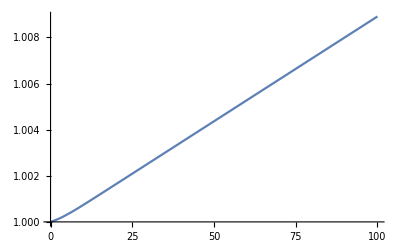

```mathematica
Plot[ωF[t,ν,μ,δ]/.{ν->0.11*100000,μ->2,δ->0.5},{t,0,100}]
```